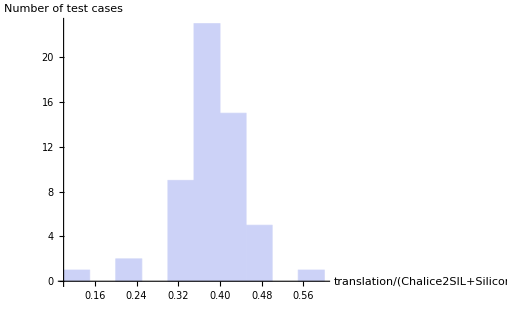

```mathematica
raw="46%
44%
39%
33%
39%
44%
37%
13%
38%
37%
40%
38%
42%
38%
39%
42%
46%
43%
37%
37%
45%
49%
42%
55%
40%
38%
34%
31%
39%
36%
32%
44%
45%
33%
41%
39%
44%
42%
39%
37%
39%
36%
34%
42%
42%
40%
39%
32%
34%
37%
21%
21%
33%
37%
36%
36%";
data=ToExpression[StringTrim[#,"%"]]/100&/@StringSplit[raw,"\n"];
Histogram[data,AxesLabel->{("translation")/("Chalice2SIL+Silicon*"),"Number of test cases"}]
```

```mathematica
84/56
```

3/2

## Full ratio

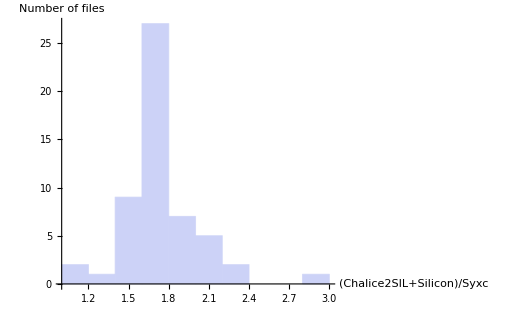

{3.69,5.02}

{3.69,5.02}

```mathematica
raw2="164%
163%
168%
178%
175%
160%
164%

165%
167%
170%
176%
191%
171%

152%
173%


170%
200%

218%
239%
237%
283%
369%
502%
155%

204%
143%
171%

113%
126%
154%
149%
158%
100%
170%
185%
192%
186%
181%
157%

163%

178%



167%


171%

143%
168%
164%
172%



212%


159%

169%
183%
183%


165%
169%




166%
206%

";
data=ToExpression[#]/100 &/@Select[StringTrim[StringSplit[raw2,"\n"],"%"],#≠""&];
split=3;
Histogram[Select[data,#<split&],AxesLabel->{("Chalice2SIL+Silicon")/("Syxc"),"Number of files"}]
Select[data,#≥split&]//N
```

```mathematica
£
```

## Excluding Chalice

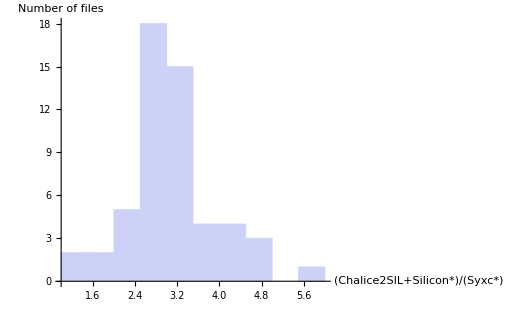

{9.57,8.83}

```mathematica
raw3="273%
285%
295%
327%
309%
245%
284%

268%
334%
312%
291%
324%
364%

229%
267%


322%
457%

446%
471%
560%
445%
957%
883%
277%

388%
177%
265%

122%
152%
271%
216%
258%
100%
321%
423%
325%
285%
342%
281%

261%

340%



268%


326%

216%
263%
297%
413%



457%


235%

337%
365%
365%


315%
325%




264%
344%

";
data=ToExpression[#]/100 &/@Select[StringTrim[StringSplit[raw3,"\n"],"%"],#≠""&];
split=6;
Histogram[Select[data,#<split&],9,AxesLabel->{("Chalice2SIL+Silicon*")/("Syxc*"),"Number of files"}]
Select[data,#≥split&]//N
```